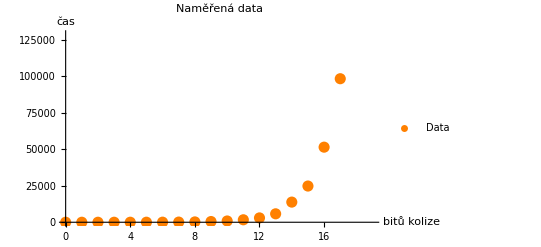

{a→0.728678,b→1.00253}

Model doby hledání x bitů kolize: 0.728678 2^(1.00253 x)

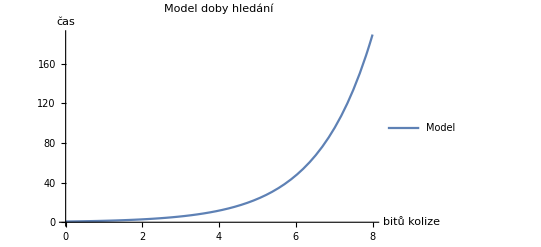

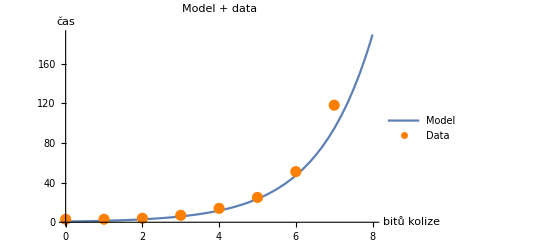

512 bitů kolize se bude hledat: 2.40039×10^154

```mathematica
data={
{0, 3},
{1, 3},
{2, 4},
{3, 7},
{4, 14},
{5, 25},
{6, 51},
{7, 118},
{8, 230},
{9, 493},
{10, 862},
{11, 1695},
{12, 2974},
{13, 5771},
{14, 13784},
{15, 24773},
{16, 51370},
{17, 98196},
{18, 195117},
{19, 395723}
};

varListPlot=ListPlot[data,PlotLabel->"Naměřená data",AxesLabel->{"bitů kolize","čas"},PlotStyle->{Orange,PointSize[0.02]},PlotLegends->{"Data"}]

(*funkce,která nám bude modelovat dobu hledání*)
function:=a*2^(b*x)

(*nalezení parametrů a,b*)
foundVars=FindFit[data,function,{a,b},{x}]

(*dosazení parametrů do funkce*)
foundFunction:=function/. foundVars
Print["Model doby hledání x bitů kolize: ",foundFunction]

(*vykreslíme model*)
plotFunction=Plot[foundFunction,{x,0,8},PlotLabel->"Model doby hledání",AxesLabel->{"bitů kolize","čas"},PlotLegends->{"Model"}]

(*vykreslíme model a přes ně naměřená data (zda model sedí)*)
Show[plotFunction,varListPlot,PlotLabel->"Model + data"]

(*Doba hledání plné kolize:do funkce dosadíme x=512*)
Print["512 bitů kolize se bude hledat: ",foundFunction/. x->512]
```